```mathematica
(* SI units *)
tausyn = 50 10^-3;(*s*)
taumemb = 20 10^-3;(*s*)
taurefr = 5 10^-3;(*s*)
noise = 5;(*mV*)
rho0=50;(*Hz*)
thresh=15 ;(*mV*)
infinityVal = 1.0;(*s*)
infinityValLong = 10.0;(*s*)
```

```mathematica
(* For numerical solution of integral equation *)
fullt = 1.0;(*s*)
dt = 1 10^-3;(*s*)
(*assume rho decays by this time*)
rhodecaytime = 0.1;(*s*)
tpoints = IntegerPart[fullt/dt];
mpoints = IntegerPart[rhodecaytime/dt];
```

```mathematica
(* synaptic and membrane kernels *)
(* ensure that you call the kernels inside integrals which don't use their negative time parts, as I'm not using a HevisideTheta[t] here. *)
kernelsyn[t_]:=Exp[-t/tausyn]/tausyn;(*integral normalized to 1*)
kernelmemb[t_]:=Exp[-t/taumemb]/taumemb;
kernelsm[t_]:=∫_-infinityVal^t kernelsyn[tau]*kernelmemb[t-tau]ⅆtau;
kernelsmList=Array[kernelsm,{IntegerPart[rhodecaytime/dt]},{0,rhodecaytime}];(* create kernellist for later *)
kernelsmInt=∫_0^infinityVal kernelsm[t]ⅆt;
eta[t_]:=Exp[-t/taurefr];
rho[h_,t_,that_]:=rho0*Exp[(h-eta[t-that]-thresh)/noise];
```

```mathematica
survivor[h_,t_,that_]:=Exp[-∫_-infinityVal^t rho[h,tprime,that]ⅆtprime];
PISI[h_,t_,that_]:=rho[h,t,that] survivor[h,t,that];
```

```mathematica
rate0=10;(*Hz*)
ratemod = 5;(*Hz*)
rate[t_]:=rate0+ratemod Sin[2*Pi*5*t];
h0=rate0 kernelsmInt;
h[tidx_]:=dt Sum[kernelsmList⟦tidx-i⟧rate[i*dt],{i,tidx-IntegerPart[rhodecaytime/dt],tidx-1}];
harray=Array[h,tpoints];
```

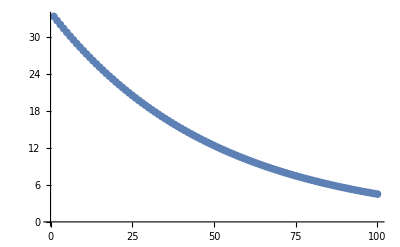

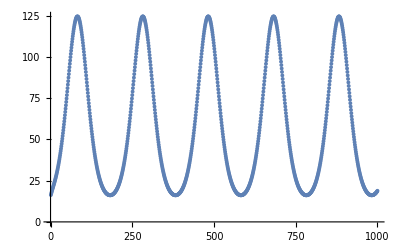

```mathematica
ListPlot[{kernelsmList}]
ListPlot[{Table[rho[harray⟦i⟧,i*dt,0],{i,tpoints}]}]
```

```mathematica
mvec=Table[0.0,{mpoints}];
mvec⟦1⟧=1.0;(* all neurons have just fired *)
Avec= Table[0.0,{tpoints}];
For[i=1,i<tpoints,i++,
hhere = harray⟦i⟧;
For[k=mpoints,k≥2,k--,
mvec⟦k⟧=mvec⟦k-1⟧Exp[-rho[hhere,i*dt,(i-k)*dt]dt];
];
mvec⟦1⟧=1-Total[mvec]+mvec⟦1⟧;(*Caution: Don't subtract mvec[[1]]*)
Avec⟦i⟧=mvec⟦1⟧/dt;
];
```

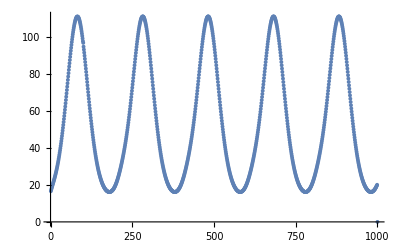

```mathematica
ListPlot[{Avec}]
```

```mathematica
rho0fn[t_]:=Exp[-Exp[-t/tau]];
FourierTransform[rho0fn[t],t,ω]
```

FourierTransform[ⅇ^(-ⅇ^(-t/tau)),t,ω]

```mathematica
S0fn[t_]:=Exp[-∫_0^t rho0fn[tprime]ⅆtprime];
FourierTransform[D[S0fn[t],t],t,ω]
```

Undefined

```mathematica
P0fn[t_]:=rho0fn[t]*S0fn[t];
FourierTransform[P0fn[t],t,ω]
```

Undefined